System defined

NDSolve`Iterate::evcvmit: -- Message text not found -- (r) (1.42263×10^6) (1.42263×10^6) (100)

-Graphics-

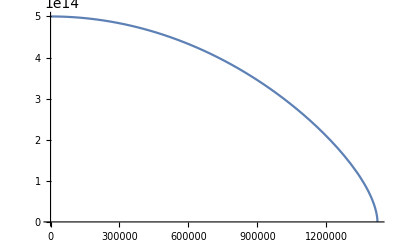

-Graphics-

Radius=1.42263×10^6

Mass=3.00588×10^33

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
G:=6.6742*10^(-8);
c:=2.99792458*10^(10);
(*G:=1;
c:=1;*)
γ:=2.75;
K:=1.982*10^(-6);
ρc:=5.0*10^(14);
(*γ:=0.3;
K:=1;
ρc:=1;*)
pc:=K*ρc^(γ);
r0:=10^(-4);

ρ[r_]=d[r];
p[r_]=K*(d[r])^(γ);
(*ϵ[r_]=p[r]/((γ-1)ρ[r])*)
ϵ[r_]=0;

eqnM:={m'[r]==4 π r^2 ρ[r](1+ϵ[r]/(c^2))};
condM:={m[r0]==0};

eqnP:={-p'[r]==G*(ρ[r]*(1+ϵ[r]/(c^2))+p[r]/(c^2))*(m[r]+4 π* r^3 *p[r]/(c^2))/(r^2*(1-2 *G* m[r]/(r*c^2)))};
condP:={p[r0]==pc};
condρ:={ρ[r0]==ρc};
stopCond:={WhenEvent[Evaluate[Re[d[r]]≤ρc/10000],rMax=r;"StopIntegration"]}

system:=Join[eqnM,eqnP,condM,condρ,stopCond];
Print["System defined"];
Do[
state=First[NDSolve`ProcessEquations[system, {m,d}, {r, r0, ∞}]];
NDSolve`Iterate[state,∞];
sol=NDSolve`ProcessSolutions[state];

(*Plot[Evaluate[m[r]/.sol],{r,r0,rMax},PlotRange->All]
Plot[Evaluate[d[r]/.sol],{r,r0,rMax},PlotRange->All]
Plot[Evaluate[p[r]/.sol],{r,r0,rMax},PlotRange->All]*)
Print["Radius=",rMax,""];
Print["Mass=",Evaluate[m[rMax]/.sol],""];
```